```mathematica
n =4;

Euler[y0_,t0_,T_,n_]:=(
y = Table[0,n+1];
h=1/n;
y[[1]] = y0;
For[i=1,i<n+1,i++,
y[[i+1]]=y[[i]] + 10 *h* y[[i]]*( 1 - y[[i]])];
y
)
resul0=Euler[0.01,0,1,4]
```

{0.01,0.03475,0.118606,0.379953,0.968924}

1

```mathematica
n =50;

Euler[y0_,t0_,T_,n_]:=(
y = Table[0,n+1];
h=1/n;
y[[1]] = y0;
For[i=1,i<n+1,i++,
y[[i+1]]=y[[i]] + 10 *h* y[[i]]*( 1 - y[[i]])];
y
)
result1=Euler[0.01,0,1,50]
```

{0.01,0.01198,0.0143473,0.0171756,0.0205517,0.0245776,0.0293723,0.0350742,0.041843,0.0498614,0.0593365,0.0704996,0.0836055,0.0989286,0.116757,0.137382,0.161083,0.188111,0.218656,0.252825,0.290606,0.331836,0.376181,0.423114,0.471932,0.521774,0.57168,0.620652,0.667741,0.712113,0.753115,0.790301,0.823446,0.852523,0.877668,0.899142,0.917279,0.932455,0.945051,0.955437,0.963952,0.970902,0.976552,0.981132,0.984834,0.987821,0.990228,0.992163,0.993718,0.994967,0.995968}

2

```mathematica
n =250;

Euler[y0_,t0_,T_,n_]:=(
y = Table[0,n+1];
h=1/n;
y[[1]] = y0;
For[i=1,i<n+1,i++,
y[[i+1]]=y[[i]] + 10 *h* y[[i]]*( 1 - y[[i]])];
y
)
result2=Euler[0.01,0,1,250]
```

{0.01,0.010396,0.0108075,0.0112351,0.0116795,0.0121412,0.012621,0.0131194,0.0136373,0.0141754,0.0147344,0.0153151,0.0159183,0.0165449,0.0171957,0.0178717,0.0185738,0.019303,0.0200602,0.0208465,0.021663,0.0225107,0.0233909,0.0243046,0.0252532,0.0262378,0.0272598,0.0283204,0.0294212,0.0305634,0.0317486,0.0329782,0.0342538,0.0355771,0.0369495,0.0383729,0.0398489,0.0413793,0.042966,0.0446108,0.0463156,0.0480825,0.0499133,0.0518102,0.0537752,0.0558105,0.0579184,0.0601009,0.0623605,0.0646993,0.0671199,0.0696244,0.0722155,0.0748955,0.077667,0.0805324,0.0834943,0.0865552,0.0897177,0.0929844,0.096358,0.0998409,0.103436,0.107145,0.110972,0.114918,0.118987,0.12318,0.1275,0.13195,0.136531,0.141247,0.146099,0.151089,0.156219,0.161492,0.166909,0.172471,0.17818,0.184037,0.190044,0.196201,0.202509,0.208969,0.215581,0.222345,0.229261,0.236329,0.243548,0.250918,0.258436,0.266102,0.273914,0.281869,0.289966,0.298201,0.306572,0.315076,0.323708,0.332465,0.341342,0.350335,0.359439,0.368649,0.377959,0.387363,0.396855,0.40643,0.41608,0.425798,0.435578,0.445412,0.455293,0.465213,0.475164,0.48514,0.495131,0.50513,0.515129,0.52512,0.535094,0.545045,0.554964,0.564843,0.574675,0.584452,0.594166,0.603812,0.613381,0.622867,0.632263,0.641563,0.650761,0.659852,0.66883,0.67769,0.686427,0.695037,0.703515,0.711858,0.720063,0.728126,0.736044,0.743816,0.751438,0.758909,0.766228,0.773393,0.780403,0.787258,0.793957,0.800501,0.806889,0.813121,0.8192,0.825124,0.830896,0.836516,0.841986,0.847308,0.852483,0.857514,0.862401,0.867148,0.871756,0.876228,0.880566,0.884772,0.88885,0.892802,0.896631,0.900338,0.903927,0.907401,0.910762,0.914013,0.917157,0.920196,0.923133,0.925971,0.928713,0.931362,0.933919,0.936387,0.93877,0.941069,0.943287,0.945427,0.947491,0.949481,0.9514,0.953249,0.955032,0.95675,0.958405,0.96,0.961536,0.963015,0.96444,0.965812,0.967132,0.968404,0.969628,0.970806,0.971939,0.97303,0.97408,0.97509,0.976062,0.976996,0.977895,0.97876,0.979591,0.980391,0.98116,0.981899,0.98261,0.983294,0.983951,0.984583,0.98519,0.985773,0.986334,0.986874,0.987392,0.98789,0.988368,0.988828,0.98927,0.989695,0.990103,0.990494,0.990871,0.991233,0.991581,0.991914,0.992235,0.992543,0.992839,0.993124,0.993397,0.993659,0.993911,0.994153,0.994386,0.994609,0.994824,0.99503,0.995228,0.995418,0.9956}

3

{0.01,0.03475,0.118606,0.379953,0.968924}

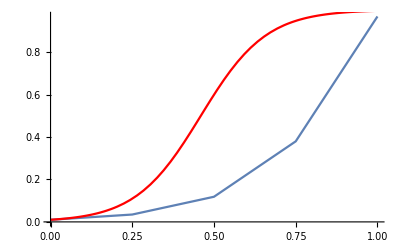

```mathematica
result0=Euler[0.01,0,1,4]
Show[{ListLinePlot[Table[{i h,result0[[i+1]]},{i,0,4}]],Plot[exactSolution[t],{t,0,1},PlotStyle->Red]}]
```

4

{0.01,0.01198,0.0143473,0.0171756,0.0205517,0.0245776,0.0293723,0.0350742,0.041843,0.0498614,0.0593365,0.0704996,0.0836055,0.0989286,0.116757,0.137382,0.161083,0.188111,0.218656,0.252825,0.290606,0.331836,0.376181,0.423114,0.471932,0.521774,0.57168,0.620652,0.667741,0.712113,0.753115,0.790301,0.823446,0.852523,0.877668,0.899142,0.917279,0.932455,0.945051,0.955437,0.963952,0.970902,0.976552,0.981132,0.984834,0.987821,0.990228,0.992163,0.993718,0.994967,0.995968}

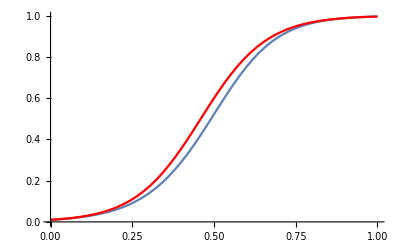

```mathematica
result1=Euler[0.01,0,1,50]
Show[{ListLinePlot[Table[{i h,result1[[i+1]]},{i,0,50}]],Plot[exactSolution[t],{t,0,1},PlotStyle->Red]}]
```

5

{0.01,0.010396,0.0108075,0.0112351,0.0116795,0.0121412,0.012621,0.0131194,0.0136373,0.0141754,0.0147344,0.0153151,0.0159183,0.0165449,0.0171957,0.0178717,0.0185738,0.019303,0.0200602,0.0208465,0.021663,0.0225107,0.0233909,0.0243046,0.0252532,0.0262378,0.0272598,0.0283204,0.0294212,0.0305634,0.0317486,0.0329782,0.0342538,0.0355771,0.0369495,0.0383729,0.0398489,0.0413793,0.042966,0.0446108,0.0463156,0.0480825,0.0499133,0.0518102,0.0537752,0.0558105,0.0579184,0.0601009,0.0623605,0.0646993,0.0671199,0.0696244,0.0722155,0.0748955,0.077667,0.0805324,0.0834943,0.0865552,0.0897177,0.0929844,0.096358,0.0998409,0.103436,0.107145,0.110972,0.114918,0.118987,0.12318,0.1275,0.13195,0.136531,0.141247,0.146099,0.151089,0.156219,0.161492,0.166909,0.172471,0.17818,0.184037,0.190044,0.196201,0.202509,0.208969,0.215581,0.222345,0.229261,0.236329,0.243548,0.250918,0.258436,0.266102,0.273914,0.281869,0.289966,0.298201,0.306572,0.315076,0.323708,0.332465,0.341342,0.350335,0.359439,0.368649,0.377959,0.387363,0.396855,0.40643,0.41608,0.425798,0.435578,0.445412,0.455293,0.465213,0.475164,0.48514,0.495131,0.50513,0.515129,0.52512,0.535094,0.545045,0.554964,0.564843,0.574675,0.584452,0.594166,0.603812,0.613381,0.622867,0.632263,0.641563,0.650761,0.659852,0.66883,0.67769,0.686427,0.695037,0.703515,0.711858,0.720063,0.728126,0.736044,0.743816,0.751438,0.758909,0.766228,0.773393,0.780403,0.787258,0.793957,0.800501,0.806889,0.813121,0.8192,0.825124,0.830896,0.836516,0.841986,0.847308,0.852483,0.857514,0.862401,0.867148,0.871756,0.876228,0.880566,0.884772,0.88885,0.892802,0.896631,0.900338,0.903927,0.907401,0.910762,0.914013,0.917157,0.920196,0.923133,0.925971,0.928713,0.931362,0.933919,0.936387,0.93877,0.941069,0.943287,0.945427,0.947491,0.949481,0.9514,0.953249,0.955032,0.95675,0.958405,0.96,0.961536,0.963015,0.96444,0.965812,0.967132,0.968404,0.969628,0.970806,0.971939,0.97303,0.97408,0.97509,0.976062,0.976996,0.977895,0.97876,0.979591,0.980391,0.98116,0.981899,0.98261,0.983294,0.983951,0.984583,0.98519,0.985773,0.986334,0.986874,0.987392,0.98789,0.988368,0.988828,0.98927,0.989695,0.990103,0.990494,0.990871,0.991233,0.991581,0.991914,0.992235,0.992543,0.992839,0.993124,0.993397,0.993659,0.993911,0.994153,0.994386,0.994609,0.994824,0.99503,0.995228,0.995418,0.9956}

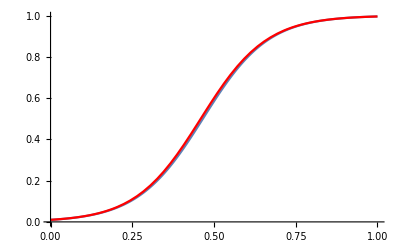

```mathematica
result2=Euler[0.01,0,1,250]
Show[{ListLinePlot[Table[{i h,result2[[i+1]]},{i,0,250}]],Plot[exactSolution[t],{t,0,1},PlotStyle->Red]}]
```

6

1/4

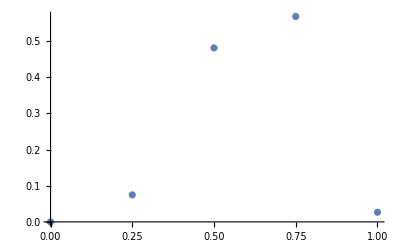

```mathematica
h0=1/4
ListPlot[Table[{i h1,Abs[exactSolution[i h0]-result0[[i+1]]]},{i,0,4}]]
```

7

1/50

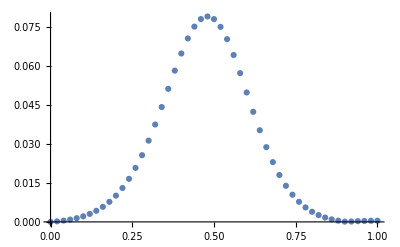

```mathematica
h1=1/50
ListPlot[Table[{i h1,Abs[exactSolution[i h1]-result1[[i+1]]]},{i,0,50}]]
```

8

1/250

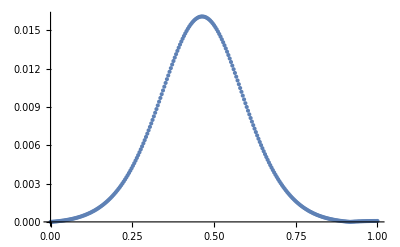

```mathematica
h2=1/250
ListPlot[Table[{i h2,Abs[exactSolution[i h2]-result2[[i+1]]]},{i,0,250}]]
```